```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
<<RLBot`
SetDirectory[NotebookDirectory[]];
```

```mathematica
{frame, ball, inputs, car} = ImportPhysicsTickJSONEpisode["boost_minimum.json"];
```

```mathematica
{frame, ball, inputs, car} = ImportPhysicsTickJSONEpisode["boost_minimum_feather.json"];
```

```mathematica
v = #["velocity"].(#["orientation"][[All, 1]]) & /@ car;
a =  (v[[2;;-1]] - v[[1;;-2]])/(frame[[2;;-1]] - frame[[1;;-2]])*120;
boost = (#["boost"]& /@ inputs) /. {True->1, False->0};
frame = frame - frame[[1]];
```

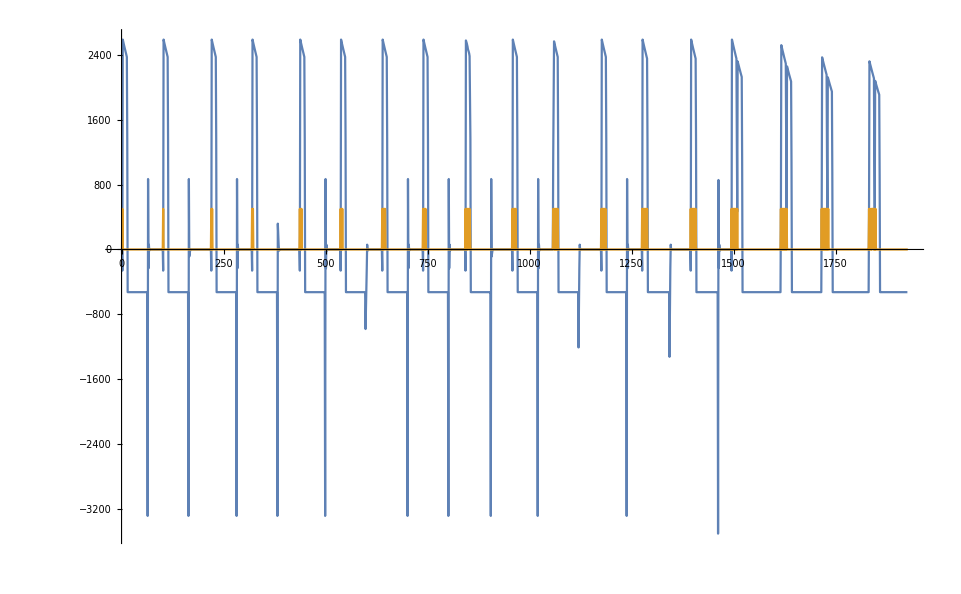

```mathematica
ListLinePlot[{
Transpose[{frame[[1;;-2]], a}], 
Transpose[{frame,500 boost}]
}, PlotRange->All]
```

```mathematica
MatrixForm[Transpose[{v, boost, frame}]]
```

(-0.0797968 | 0 | 42816
-0.0797968 | 0 | 42817
-0.0797968 | 1 | 42818
-2.25019 | 0 | 42819
19.2913 | 0 | 42820
40.6507 | 0 | 42821
61.8201 | 0 | 42822
82.8096 | 0 | 42823
103.619 | 0 | 42824
124.249 | 0 | 42825
144.708 | 0 | 42826
164.987 | 0 | 42827
185.097 | 0 | 42828
205.026 | 0 | 42829
224.786 | 0 | 42830
236.185 | 0 | 42831
231.805 | 0 | 42832
227.424 | 0 | 42833
223.044 | 0 | 42834
218.664 | 0 | 42835
214.284 | 0 | 42836
209.904 | 0 | 42837
205.524 | 0 | 42838
201.144 | 0 | 42839
196.764 | 0 | 42840
192.384 | 0 | 42841
188.005 | 0 | 42842
183.625 | 0 | 42843
179.245 | 0 | 42844
174.865 | 0 | 42845
170.485 | 0 | 42846
166.105 | 0 | 42847
161.725 | 0 | 42848
157.346 | 0 | 42849
152.966 | 0 | 42850
148.586 | 0 | 42851
144.206 | 0 | 42852
139.826 | 0 | 42853
135.446 | 0 | 42854
131.067 | 0 | 42855
126.687 | 0 | 42856
122.307 | 0 | 42857
117.927 | 0 | 42858
113.547 | 0 | 42859
109.167 | 0 | 42860
104.787 | 0 | 42861
100.408 | 0 | 42862
96.0278 | 0 | 42863
91.6479 | 0 | 42864
87.2681 | 0 | 42865
82.8882 | 0 | 42866
78.5084 | 0 | 42867
74.1286 | 0 | 42868
69.7487 | 0 | 42869
65.3689 | 0 | 42870
60.989 | 0 | 42871
56.6092 | 0 | 42872
52.2293 | 0 | 42873
47.8495 | 0 | 42874
43.4696 | 0 | 42875
39.0898 | 0 | 42876
34.71 | 0 | 42877
30.3301 | 0 | 42878
25.9503 | 0 | 42879
21.5704 | 0 | 42880
-5.77054 | 0 | 42881
1.46112 | 0 | 42882
-0.470775 | 0 | 42883
0.0211974 | 0 | 42884
-0.100796 | 0 | 42885
-0.0797968 | 0 | 42886
-0.0797968 | 0 | 42887
-0.0797968 | 0 | 42888
-0.0797968 | 0 | 42889
-0.0797968 | 0 | 42890
-0.0797968 | 0 | 42891
-0.0797968 | 0 | 42892
-0.0797968 | 0 | 42893
-0.0797968 | 0 | 42894
-0.0797968 | 0 | 42895
-0.0797968 | 0 | 42896
-0.0797968 | 0 | 42897
-0.0797968 | 0 | 42898
-0.0797968 | 0 | 42899
-0.0797968 | 0 | 42900
-0.0797968 | 0 | 42901
-0.0797968 | 0 | 42902
-0.0797968 | 0 | 42903
-0.0797968 | 0 | 42904
-0.0797968 | 0 | 42905
-0.0797968 | 0 | 42906
-0.0797968 | 0 | 42907
-0.0797968 | 0 | 42908
-0.0797968 | 0 | 42909
-0.0797968 | 0 | 42910
-0.0797968 | 0 | 42911
-0.0797968 | 0 | 42912
-0.0797968 | 0 | 42913
-0.0797968 | 0 | 42914
-0.0797968 | 0 | 42915
-0.0797968 | 0 | 42916
-0.0797968 | 0 | 42917
-0.0797968 | 1 | 42918
-2.25019 | 0 | 42919
19.2913 | 0 | 42920
40.6507 | 0 | 42921
61.8201 | 0 | 42922
82.8096 | 0 | 42923
103.619 | 0 | 42924
124.249 | 0 | 42925
144.708 | 0 | 42926
164.987 | 0 | 42927
185.097 | 0 | 42928
205.026 | 0 | 42929
224.786 | 0 | 42930
236.185 | 0 | 42931
231.805 | 0 | 42932
227.424 | 0 | 42933
223.044 | 0 | 42934
218.664 | 0 | 42935
214.284 | 0 | 42936
209.904 | 0 | 42937
205.524 | 0 | 42938
201.144 | 0 | 42939
192.384 | 0 | 42941
188.005 | 0 | 42942
183.625 | 0 | 42943
174.865 | 0 | 42945
170.485 | 0 | 42946
166.105 | 0 | 42947
157.346 | 0 | 42949
152.966 | 0 | 42950
148.586 | 0 | 42951
144.206 | 0 | 42952
135.446 | 0 | 42954
131.067 | 0 | 42955
126.687 | 0 | 42956
122.307 | 0 | 42957
113.547 | 0 | 42959
109.167 | 0 | 42960
100.408 | 0 | 42962
96.0278 | 0 | 42963
91.6479 | 0 | 42964
82.8882 | 0 | 42966
78.5084 | 0 | 42967
74.1286 | 0 | 42968
69.7487 | 0 | 42969
60.989 | 0 | 42971
56.6092 | 0 | 42972
52.2293 | 0 | 42973
43.4696 | 0 | 42975
39.0898 | 0 | 42976
34.71 | 0 | 42977
25.9503 | 0 | 42979
21.5704 | 0 | 42980
-5.77054 | 0 | 42981
1.46112 | 0 | 42982
0.0211974 | 0 | 42984
-0.100796 | 0 | 42985
-0.0797968 | 0 | 42986
-0.0797968 | 0 | 42988
-0.0797968 | 0 | 42989
-0.0797968 | 0 | 42990
-0.0797968 | 0 | 42992
-0.0797968 | 0 | 42993
-0.0797968 | 0 | 42994
-0.0797968 | 0 | 42996
-0.0797968 | 0 | 42997
-0.0797968 | 0 | 42999
-0.0797968 | 0 | 43000
-0.0797968 | 0 | 43002
-0.0797968 | 0 | 43003
-0.0797968 | 0 | 43004
-0.0797968 | 0 | 43006
-0.0797968 | 0 | 43007
-0.0797968 | 0 | 43008
-0.0797968 | 0 | 43009
-0.0797968 | 0 | 43010
-0.0797968 | 0 | 43011
-0.0797968 | 0 | 43012
-0.0797968 | 0 | 43013
-0.0797968 | 0 | 43014
-0.0797968 | 0 | 43016
-0.0797968 | 0 | 43017
-0.0797968 | 0 | 43018
-0.0797968 | 0 | 43019
-0.0797968 | 0 | 43020
-0.0797968 | 0 | 43021
-0.0797968 | 0 | 43022
-0.0797968 | 0 | 43023
-0.0797968 | 0 | 43024
-0.0797968 | 0 | 43025
-0.0797968 | 0 | 43026
-0.0797968 | 0 | 43027
-0.0797968 | 0 | 43028
-0.0797968 | 0 | 43029
-0.0797968 | 0 | 43030
-0.0797968 | 0 | 43031
-0.0797968 | 0 | 43032
-0.0797968 | 0 | 43033
-0.0797968 | 0 | 43034
-0.0797968 | 0 | 43035
-0.0797968 | 1 | 43036
-2.25019 | 0 | 43037
19.2913 | 1 | 43038
40.6507 | 0 | 43039
61.8201 | 0 | 43040
82.8096 | 0 | 43041
103.619 | 0 | 43042
124.249 | 0 | 43043
144.708 | 0 | 43044
164.987 | 0 | 43045
185.097 | 0 | 43046
205.026 | 0 | 43047
224.786 | 0 | 43048
236.185 | 0 | 43049
231.805 | 0 | 43050
227.424 | 0 | 43051
223.044 | 0 | 43052
218.664 | 0 | 43053
214.284 | 0 | 43054
209.904 | 0 | 43055
205.524 | 0 | 43056
201.144 | 0 | 43057
196.764 | 0 | 43058
192.384 | 0 | 43059
188.005 | 0 | 43060
183.625 | 0 | 43061
179.245 | 0 | 43062
174.865 | 0 | 43063
170.485 | 0 | 43064
166.105 | 0 | 43065
161.725 | 0 | 43066
157.346 | 0 | 43067
152.966 | 0 | 43068
148.586 | 0 | 43069
144.206 | 0 | 43070
139.826 | 0 | 43071
135.446 | 0 | 43072
131.067 | 0 | 43073
126.687 | 0 | 43074
122.307 | 0 | 43075
117.927 | 0 | 43076
113.547 | 0 | 43077
109.167 | 0 | 43078
104.787 | 0 | 43079
100.408 | 0 | 43080
96.0278 | 0 | 43081
91.6479 | 0 | 43082
87.2681 | 0 | 43083
82.8882 | 0 | 43084
78.5084 | 0 | 43085
74.1286 | 0 | 43086
69.7487 | 0 | 43087
65.3689 | 0 | 43088
60.989 | 0 | 43089
56.6092 | 0 | 43090
52.2293 | 0 | 43091
47.8495 | 0 | 43092
43.4696 | 0 | 43093
39.0898 | 0 | 43094
34.71 | 0 | 43095
30.3301 | 0 | 43096
25.9503 | 0 | 43097
21.5704 | 0 | 43098
-5.77054 | 0 | 43099
1.46112 | 0 | 43100
-0.470775 | 0 | 43101
0.0211974 | 0 | 43102
-0.100796 | 0 | 43103
-0.0797968 | 0 | 43104
-0.0797968 | 0 | 43105
-0.0797968 | 0 | 43106
-0.0797968 | 0 | 43107
-0.0797968 | 0 | 43108
-0.0797968 | 0 | 43109
-0.0797968 | 0 | 43110
-0.0797968 | 0 | 43111
-0.0797968 | 0 | 43112
-0.0797968 | 0 | 43113
-0.0797968 | 0 | 43114
-0.0797968 | 0 | 43115
-0.0797968 | 0 | 43116
-0.0797968 | 0 | 43117
-0.0797968 | 0 | 43118
-0.0797968 | 0 | 43119
-0.0797968 | 0 | 43120
-0.0797968 | 0 | 43121
-0.0797968 | 0 | 43122
-0.0797968 | 0 | 43123
-0.0797968 | 0 | 43124
-0.0797968 | 0 | 43125
-0.0797968 | 0 | 43126
-0.0797968 | 0 | 43127
-0.0797968 | 0 | 43128
-0.0797968 | 0 | 43129
-0.0797968 | 0 | 43130
-0.0797968 | 0 | 43131
-0.0797968 | 0 | 43132
-0.0797968 | 0 | 43133
-0.0797968 | 0 | 43134
-0.0797968 | 0 | 43135
-0.0797968 | 1 | 43136
-2.25019 | 0 | 43137
19.2913 | 1 | 43138
40.6507 | 0 | 43139
61.8201 | 0 | 43140
82.8096 | 0 | 43141
103.619 | 0 | 43142
124.249 | 0 | 43143
144.708 | 0 | 43144
164.987 | 0 | 43145
185.097 | 0 | 43146
205.026 | 0 | 43147
224.786 | 0 | 43148
236.185 | 0 | 43149
231.805 | 0 | 43150
227.424 | 0 | 43151
223.044 | 0 | 43152
218.664 | 0 | 43153
214.284 | 0 | 43154
209.904 | 0 | 43155
205.524 | 0 | 43156
201.144 | 0 | 43157
196.764 | 0 | 43158
192.384 | 0 | 43159
188.005 | 0 | 43160
183.625 | 0 | 43161
179.245 | 0 | 43162
174.865 | 0 | 43163
170.485 | 0 | 43164
166.105 | 0 | 43165
161.725 | 0 | 43166
157.346 | 0 | 43167
152.966 | 0 | 43168
148.586 | 0 | 43169
144.206 | 0 | 43170
139.826 | 0 | 43171
135.446 | 0 | 43172
131.067 | 0 | 43173
126.687 | 0 | 43174
122.307 | 0 | 43175
117.927 | 0 | 43176
113.547 | 0 | 43177
109.167 | 0 | 43178
100.408 | 0 | 43180
96.0278 | 0 | 43181
91.6479 | 0 | 43182
87.2681 | 0 | 43183
82.8882 | 0 | 43184
78.5084 | 0 | 43185
74.1286 | 0 | 43186
69.7487 | 0 | 43187
65.3689 | 0 | 43188
60.989 | 0 | 43189
56.6092 | 0 | 43190
52.2293 | 0 | 43191
47.8495 | 0 | 43192
43.4696 | 0 | 43193
39.0898 | 0 | 43194
34.71 | 0 | 43195
25.9503 | 0 | 43197
21.5704 | 0 | 43198
-5.77054 | 0 | 43199
-0.470775 | 0 | 43201
0.0211974 | 0 | 43202
-0.100796 | 0 | 43203
-0.0797968 | 0 | 43205
-0.0797968 | 0 | 43206
-0.0797968 | 0 | 43208
-0.0797968 | 0 | 43209
-0.0797968 | 0 | 43211
-0.0797968 | 0 | 43212
-0.0797968 | 0 | 43213
-0.0797968 | 0 | 43215
-0.0797968 | 0 | 43216
-0.0797968 | 0 | 43217
-0.0797968 | 0 | 43218
-0.0797968 | 0 | 43220
-0.0797968 | 0 | 43221
-0.0797968 | 0 | 43223
-0.0797968 | 0 | 43224
-0.0797968 | 0 | 43226
-0.0797968 | 0 | 43227
-0.0797968 | 0 | 43229
-0.0797968 | 0 | 43230
-0.0797968 | 0 | 43231
-0.0797968 | 0 | 43233
-0.0797968 | 0 | 43234
-0.0797968 | 0 | 43236
-0.0797968 | 0 | 43237
-0.0797968 | 0 | 43239
-0.0797968 | 0 | 43240
-0.0797968 | 0 | 43241
-0.0797968 | 0 | 43243
-0.0797968 | 0 | 43244
-0.0797968 | 0 | 43245
-0.0797968 | 0 | 43246
-0.0797968 | 0 | 43248
-0.0797968 | 0 | 43249
-0.0797968 | 0 | 43250
-0.0797968 | 0 | 43252
-0.0797968 | 1 | 43253
-2.25019 | 0 | 43254
19.2913 | 0 | 43255
40.6507 | 0 | 43256
61.8201 | 1 | 43257
82.8096 | 0 | 43258
103.619 | 0 | 43259
124.249 | 0 | 43260
144.708 | 0 | 43261
164.987 | 0 | 43262
185.097 | 0 | 43263
205.026 | 0 | 43264
224.786 | 0 | 43265
236.185 | 0 | 43266
231.805 | 0 | 43267
227.424 | 0 | 43268
223.044 | 0 | 43269
218.664 | 0 | 43270
214.284 | 0 | 43271
209.904 | 0 | 43272
205.524 | 0 | 43273
201.144 | 0 | 43274
196.764 | 0 | 43275
192.384 | 0 | 43276
188.005 | 0 | 43277
183.625 | 0 | 43278
179.245 | 0 | 43279
174.865 | 0 | 43280
170.485 | 0 | 43281
166.105 | 0 | 43282
161.725 | 0 | 43283
157.346 | 0 | 43284
152.966 | 0 | 43285
148.586 | 0 | 43286
144.206 | 0 | 43287
139.826 | 0 | 43288
135.446 | 0 | 43289
131.067 | 0 | 43290
126.687 | 0 | 43291
122.307 | 0 | 43292
117.927 | 0 | 43293
113.547 | 0 | 43294
109.167 | 0 | 43295
104.787 | 0 | 43296
100.408 | 0 | 43297
96.0278 | 0 | 43298
91.6479 | 0 | 43299
87.2681 | 0 | 43300
82.8882 | 0 | 43301
78.5084 | 0 | 43302
74.1286 | 0 | 43303
69.7487 | 0 | 43304
65.3689 | 0 | 43305
60.989 | 0 | 43306
56.6092 | 0 | 43307
52.2293 | 0 | 43308
47.8495 | 0 | 43309
43.4696 | 0 | 43310
39.0898 | 0 | 43311
34.71 | 0 | 43312
30.3301 | 0 | 43313
25.9503 | 0 | 43314
21.5704 | 0 | 43315
-5.77054 | 0 | 43316
1.46112 | 0 | 43317
-0.470775 | 0 | 43318
0.0211974 | 0 | 43319
-0.100796 | 0 | 43320
-0.0797968 | 0 | 43321
-0.0797968 | 0 | 43322
-0.0797968 | 0 | 43323
-0.0797968 | 0 | 43324
-0.0797968 | 0 | 43325
-0.0797968 | 0 | 43326
-0.0797968 | 0 | 43327
-0.0797968 | 0 | 43328
-0.0797968 | 0 | 43329
-0.0797968 | 0 | 43330
-0.0797968 | 0 | 43331
-0.0797968 | 0 | 43332
-0.0797968 | 0 | 43333
-0.0797968 | 0 | 43334
-0.0797968 | 0 | 43335
-0.0797968 | 0 | 43336
-0.0797968 | 0 | 43337
-0.0797968 | 0 | 43338
-0.0797968 | 0 | 43339
-0.0797968 | 0 | 43340
-0.0797968 | 0 | 43341
-0.0797968 | 0 | 43342
-0.0797968 | 0 | 43343
-0.0797968 | 0 | 43344
-0.0797968 | 0 | 43345
-0.0797968 | 0 | 43346
-0.0797968 | 0 | 43347
-0.0797968 | 0 | 43348
-0.0797968 | 0 | 43349
-0.0797968 | 0 | 43350
-0.0797968 | 0 | 43351
-0.0797968 | 0 | 43352
-0.0797968 | 1 | 43353
-2.25019 | 0 | 43354
19.2913 | 1 | 43355
40.6507 | 0 | 43356
61.8201 | 1 | 43357
82.8096 | 0 | 43358
103.619 | 0 | 43359
124.249 | 0 | 43360
144.708 | 0 | 43361
164.987 | 0 | 43362
185.097 | 0 | 43363
205.026 | 0 | 43364
224.786 | 0 | 43365
236.185 | 0 | 43366
231.805 | 0 | 43367
227.424 | 0 | 43368
223.044 | 0 | 43369
218.664 | 0 | 43370
214.284 | 0 | 43371
209.904 | 0 | 43372
205.524 | 0 | 43373
201.144 | 0 | 43374
196.764 | 0 | 43375
192.384 | 0 | 43376
188.005 | 0 | 43377
183.625 | 0 | 43378
179.245 | 0 | 43379
174.865 | 0 | 43380
170.485 | 0 | 43381
166.105 | 0 | 43382
161.725 | 0 | 43383
157.346 | 0 | 43384
152.966 | 0 | 43385
148.586 | 0 | 43386
144.206 | 0 | 43387
139.826 | 0 | 43388
135.446 | 0 | 43389
131.067 | 0 | 43390
126.687 | 0 | 43391
122.307 | 0 | 43392
117.927 | 0 | 43393
113.547 | 0 | 43394
109.167 | 0 | 43395
104.787 | 0 | 43396
100.408 | 0 | 43397
96.0278 | 0 | 43398
91.6479 | 0 | 43399
87.2681 | 0 | 43400
82.8882 | 0 | 43401
78.5084 | 0 | 43402
74.1286 | 0 | 43403
69.7487 | 0 | 43404
65.3689 | 0 | 43405
60.989 | 0 | 43406
56.6092 | 0 | 43407
52.2293 | 0 | 43408
47.8495 | 0 | 43409
43.4696 | 0 | 43410
39.0898 | 0 | 43411
34.71 | 0 | 43412
30.3301 | 0 | 43413
25.9503 | 0 | 43414
1.46112 | 0 | 43417
-0.470775 | 0 | 43418
0.0211974 | 0 | 43419
-0.100796 | 0 | 43420
-0.0797968 | 0 | 43421
-0.0797968 | 0 | 43422
-0.0797968 | 0 | 43423
-0.0797968 | 0 | 43424
-0.0797968 | 0 | 43425
-0.0797968 | 0 | 43426
-0.0797968 | 0 | 43427
-0.0797968 | 0 | 43428
-0.0797968 | 0 | 43429
-0.0797968 | 0 | 43430
-0.0797968 | 0 | 43431
-0.0797968 | 0 | 43432
-0.0797968 | 0 | 43433
-0.0797968 | 0 | 43434
-0.0797968 | 0 | 43435
-0.0797968 | 0 | 43436
-0.0797968 | 0 | 43437
-0.0797968 | 0 | 43438
-0.0797968 | 0 | 43439
-0.0797968 | 0 | 43440
-0.0797968 | 0 | 43441
-0.0797968 | 0 | 43442
-0.0797968 | 0 | 43443
-0.0797968 | 0 | 43444
-0.0797968 | 0 | 43445
-0.0797968 | 0 | 43446
-0.0797968 | 0 | 43447
-0.0797968 | 0 | 43448
-0.0797968 | 0 | 43449
-0.0797968 | 0 | 43450
-0.0797968 | 0 | 43451
-0.0797968 | 0 | 43452
-0.0797968 | 0 | 43453
-0.0797968 | 0 | 43454
-0.0797968 | 1 | 43455
-2.25019 | 0 | 43456
19.2913 | 1 | 43457
40.6507 | 0 | 43458
61.8201 | 1 | 43459
82.8096 | 0 | 43460
103.619 | 1 | 43461
124.249 | 1 | 43462
144.708 | 0 | 43463
164.987 | 0 | 43464
185.097 | 0 | 43465
205.026 | 0 | 43466
224.786 | 0 | 43467
236.185 | 0 | 43468
231.805 | 0 | 43469
227.424 | 0 | 43470
223.044 | 0 | 43471
218.664 | 0 | 43472
214.284 | 0 | 43473
209.904 | 0 | 43474
205.524 | 0 | 43475
201.144 | 0 | 43476
196.764 | 0 | 43477
192.384 | 0 | 43478
188.005 | 0 | 43479
183.625 | 0 | 43480
179.245 | 0 | 43481
174.865 | 0 | 43482
170.485 | 0 | 43483
166.105 | 0 | 43484
161.725 | 0 | 43485
157.346 | 0 | 43486
152.966 | 0 | 43487
148.586 | 0 | 43488
144.206 | 0 | 43489
139.826 | 0 | 43490
135.446 | 0 | 43491
131.067 | 0 | 43492
126.687 | 0 | 43493
122.307 | 0 | 43494
117.927 | 0 | 43495
113.547 | 0 | 43496
109.167 | 0 | 43497
104.787 | 0 | 43498
100.408 | 0 | 43499
96.0278 | 0 | 43500
91.6479 | 0 | 43501
87.2681 | 0 | 43502
82.8882 | 0 | 43503
78.5084 | 0 | 43504
74.1286 | 0 | 43505
69.7487 | 0 | 43506
65.3689 | 0 | 43507
60.989 | 0 | 43508
56.6092 | 0 | 43509
52.2293 | 0 | 43510
47.8495 | 0 | 43511
43.4696 | 0 | 43512
39.0898 | 0 | 43513
34.71 | 0 | 43514
30.3301 | 0 | 43515
25.9503 | 0 | 43516
21.5704 | 0 | 43517
-5.77054 | 0 | 43518
1.46112 | 0 | 43519
-0.470775 | 0 | 43520
0.0211974 | 0 | 43521
-0.100796 | 0 | 43522
-0.0797968 | 0 | 43523
-0.0797968 | 0 | 43524
-0.0797968 | 0 | 43525
-0.0797968 | 0 | 43526
-0.0797968 | 0 | 43527
-0.0797968 | 0 | 43528
-0.0797968 | 0 | 43529
-0.0797968 | 0 | 43530
-0.0797968 | 0 | 43531
-0.0797968 | 0 | 43532
-0.0797968 | 0 | 43533
-0.0797968 | 0 | 43534
-0.0797968 | 0 | 43535
-0.0797968 | 0 | 43536
-0.0797968 | 0 | 43537
-0.0797968 | 0 | 43538
-0.0797968 | 0 | 43539
-0.0797968 | 0 | 43540
-0.0797968 | 0 | 43541
-0.0797968 | 0 | 43542
-0.0797968 | 0 | 43543
-0.0797968 | 0 | 43544
-0.0797968 | 0 | 43545
-0.0797968 | 0 | 43546
-0.0797968 | 0 | 43547
-0.0797968 | 0 | 43548
-0.0797968 | 0 | 43549
-0.0797968 | 0 | 43550
-0.0797968 | 0 | 43551
-0.0797968 | 0 | 43552
-0.0797968 | 0 | 43553
-0.0797968 | 0 | 43554
-0.0797968 | 1 | 43555
-2.25019 | 0 | 43556
19.2913 | 1 | 43557
40.6507 | 0 | 43558
61.8201 | 1 | 43559
82.8096 | 0 | 43560
103.619 | 1 | 43561
124.249 | 0 | 43562
144.708 | 0 | 43563
164.987 | 0 | 43564
185.097 | 0 | 43565
205.026 | 0 | 43566
224.786 | 0 | 43567
236.185 | 0 | 43568
231.805 | 0 | 43569
227.424 | 0 | 43570
223.044 | 0 | 43571
218.664 | 0 | 43572
214.284 | 0 | 43573
209.904 | 0 | 43574
205.524 | 0 | 43575
201.144 | 0 | 43576
196.764 | 0 | 43577
192.384 | 0 | 43578
188.005 | 0 | 43579
183.625 | 0 | 43580
179.245 | 0 | 43581
174.865 | 0 | 43582
170.485 | 0 | 43583
166.105 | 0 | 43584
161.725 | 0 | 43585
157.346 | 0 | 43586
152.966 | 0 | 43587
148.586 | 0 | 43588
144.206 | 0 | 43589
139.826 | 0 | 43590
135.446 | 0 | 43591
131.067 | 0 | 43592
126.687 | 0 | 43593
122.307 | 0 | 43594
117.927 | 0 | 43595
113.547 | 0 | 43596
109.167 | 0 | 43597
104.787 | 0 | 43598
100.408 | 0 | 43599
96.0278 | 0 | 43600
91.6479 | 0 | 43601
87.2681 | 0 | 43602
82.8882 | 0 | 43603
78.5084 | 0 | 43604
74.1286 | 0 | 43605
69.7487 | 0 | 43606
65.3689 | 0 | 43607
60.989 | 0 | 43608
56.6092 | 0 | 43609
52.2293 | 0 | 43610
47.8495 | 0 | 43611
43.4696 | 0 | 43612
39.0898 | 0 | 43613
34.71 | 0 | 43614
30.3301 | 0 | 43615
25.9503 | 0 | 43616
21.5704 | 0 | 43617
-5.77054 | 0 | 43618
1.46112 | 0 | 43619
-0.470775 | 0 | 43620
0.0211974 | 0 | 43621
-0.100796 | 0 | 43622
-0.0797968 | 0 | 43623
-0.0797968 | 0 | 43624
-0.0797968 | 0 | 43625
-0.0797968 | 0 | 43626
-0.0797968 | 0 | 43627
-0.0797968 | 0 | 43628
-0.0797968 | 0 | 43629
-0.0797968 | 0 | 43630
-0.0797968 | 0 | 43631
-0.0797968 | 0 | 43632
-0.0797968 | 0 | 43633
-0.0797968 | 0 | 43634
-0.0797968 | 0 | 43635
-0.0797968 | 0 | 43636
-0.0797968 | 0 | 43637
-0.0797968 | 0 | 43638
-0.0797968 | 0 | 43639
-0.0797968 | 0 | 43640
-0.0797968 | 0 | 43641
-0.0797968 | 0 | 43642
-0.0797968 | 0 | 43643
-0.0797968 | 0 | 43644
-0.0797968 | 0 | 43646
-0.0797968 | 0 | 43647
-0.0797968 | 0 | 43648
-0.0797968 | 0 | 43649
-0.0797968 | 0 | 43650
-0.0797968 | 0 | 43652
-0.0797968 | 0 | 43653
-0.0797968 | 0 | 43655
-0.0797968 | 0 | 43656
-0.0797968 | 0 | 43658
-0.0797968 | 1 | 43659
-2.25019 | 0 | 43660
40.6507 | 1 | 43662
61.8201 | 0 | 43663
82.8096 | 1 | 43664
103.619 | 0 | 43665
144.708 | 1 | 43667
164.987 | 0 | 43668
185.097 | 1 | 43669
224.786 | 0 | 43671
236.185 | 0 | 43672
231.805 | 0 | 43673
223.044 | 0 | 43675
218.664 | 0 | 43676
209.904 | 0 | 43678
205.524 | 0 | 43679
196.764 | 0 | 43681
192.384 | 0 | 43682
188.005 | 0 | 43683
179.245 | 0 | 43685
174.865 | 0 | 43686
170.485 | 0 | 43687
161.725 | 0 | 43689
157.346 | 0 | 43690
152.966 | 0 | 43691
144.206 | 0 | 43693
139.826 | 0 | 43694
131.067 | 0 | 43696
126.687 | 0 | 43697
117.927 | 0 | 43699
113.547 | 0 | 43700
109.167 | 0 | 43701
100.408 | 0 | 43703
96.0278 | 0 | 43704
91.6479 | 0 | 43705
82.8882 | 0 | 43707
78.5084 | 0 | 43708
74.1286 | 0 | 43709
65.3689 | 0 | 43711
60.989 | 0 | 43712
56.6092 | 0 | 43713
52.2293 | 0 | 43714
47.8495 | 0 | 43715
43.4696 | 0 | 43716
39.0898 | 0 | 43717
34.71 | 0 | 43718
30.3301 | 0 | 43719
25.9503 | 0 | 43720
21.5704 | 0 | 43721
-5.77054 | 0 | 43722
1.46112 | 0 | 43723
0.0211974 | 0 | 43725
-0.100796 | 0 | 43726
-0.0797968 | 0 | 43727
-0.0797968 | 0 | 43728
-0.0797968 | 0 | 43729
-0.0797968 | 0 | 43730
-0.0797968 | 0 | 43731
-0.0797968 | 0 | 43732
-0.0797968 | 0 | 43733
-0.0797968 | 0 | 43734
-0.0797968 | 0 | 43735
-0.0797968 | 0 | 43736
-0.0797968 | 0 | 43737
-0.0797968 | 0 | 43738
-0.0797968 | 0 | 43739
-0.0797968 | 0 | 43740
-0.0797968 | 0 | 43741
-0.0797968 | 0 | 43742
-0.0797968 | 0 | 43743
-0.0797968 | 0 | 43744
-0.0797968 | 0 | 43745
-0.0797968 | 0 | 43746
-0.0797968 | 0 | 43747
-0.0797968 | 0 | 43748
-0.0797968 | 0 | 43749
-0.0797968 | 0 | 43750
-0.0797968 | 0 | 43751
-0.0797968 | 0 | 43752
-0.0797968 | 0 | 43753
-0.0797968 | 0 | 43754
-0.0797968 | 0 | 43755
-0.0797968 | 0 | 43756
-0.0797968 | 0 | 43757
-0.0797968 | 0 | 43758
-0.0797968 | 0 | 43759
-0.0797968 | 0 | 43760
-0.0797968 | 0 | 43761
-0.0797968 | 0 | 43762
-0.0797968 | 0 | 43763
-0.0797968 | 0 | 43764
-0.0797968 | 0 | 43765
-0.0797968 | 0 | 43766
-0.0797968 | 0 | 43767
-0.0797968 | 0 | 43768
-0.0797968 | 0 | 43769
-0.0797968 | 0 | 43770
-0.0797968 | 0 | 43771
-0.0797968 | 0 | 43772
-0.0797968 | 0 | 43773
-0.0797968 | 1 | 43774
-2.25019 | 0 | 43775
19.2913 | 1 | 43776
40.6507 | 0 | 43777
61.8201 | 1 | 43778
82.8096 | 0 | 43779
103.619 | 1 | 43780
124.249 | 0 | 43781
144.708 | 1 | 43782
164.987 | 0 | 43783
185.097 | 0 | 43784
205.026 | 0 | 43785
224.786 | 0 | 43786
236.185 | 0 | 43787
231.805 | 0 | 43788
227.424 | 0 | 43789
223.044 | 0 | 43790
218.664 | 0 | 43791
214.284 | 0 | 43792
209.904 | 0 | 43793
205.524 | 0 | 43794
201.144 | 0 | 43795
196.764 | 0 | 43796
192.384 | 0 | 43797
188.005 | 0 | 43798
183.625 | 0 | 43799
179.245 | 0 | 43800
174.865 | 0 | 43801
170.485 | 0 | 43802
166.105 | 0 | 43803
161.725 | 0 | 43804
157.346 | 0 | 43805
152.966 | 0 | 43806
148.586 | 0 | 43807
144.206 | 0 | 43808
139.826 | 0 | 43809
135.446 | 0 | 43810
131.067 | 0 | 43811
126.687 | 0 | 43812
122.307 | 0 | 43813
117.927 | 0 | 43814
113.547 | 0 | 43815
109.167 | 0 | 43816
104.787 | 0 | 43817
100.408 | 0 | 43818
96.0278 | 0 | 43819
91.6479 | 0 | 43820
87.2681 | 0 | 43821
82.8882 | 0 | 43822
78.5084 | 0 | 43823
74.1286 | 0 | 43824
69.7487 | 0 | 43825
65.3689 | 0 | 43826
60.989 | 0 | 43827
56.6092 | 0 | 43828
52.2293 | 0 | 43829
47.8495 | 0 | 43830
43.4696 | 0 | 43831
39.0898 | 0 | 43832
34.71 | 0 | 43833
30.3301 | 0 | 43834
25.9503 | 0 | 43835
21.5704 | 0 | 43836
-5.77054 | 0 | 43837
1.46112 | 0 | 43838
-0.470775 | 0 | 43839
0.0211974 | 0 | 43840
-0.100796 | 0 | 43841
-0.0797968 | 0 | 43842
-0.0797968 | 0 | 43843
-0.0797968 | 0 | 43844
-0.0797968 | 0 | 43845
-0.0797968 | 0 | 43846
-0.0797968 | 0 | 43847
-0.0797968 | 0 | 43848
-0.0797968 | 0 | 43849
-0.0797968 | 0 | 43850
-0.0797968 | 0 | 43851
-0.0797968 | 0 | 43852
-0.0797968 | 0 | 43853
-0.0797968 | 0 | 43854
-0.0797968 | 0 | 43855
-0.0797968 | 0 | 43856
-0.0797968 | 0 | 43857
-0.0797968 | 0 | 43858
-0.0797968 | 0 | 43859
-0.0797968 | 0 | 43860
-0.0797968 | 0 | 43861
-0.0797968 | 0 | 43862
-0.0797968 | 0 | 43863
-0.0797968 | 0 | 43864
-0.0797968 | 0 | 43865
-0.0797968 | 0 | 43866
-0.0797968 | 0 | 43867
-0.0797968 | 0 | 43868
-0.0797968 | 0 | 43869
-0.0797968 | 0 | 43870
-0.0797968 | 0 | 43871
-0.0797968 | 0 | 43872
-0.0797968 | 0 | 43873
-0.0797968 | 1 | 43874
19.2913 | 0 | 43876
40.6507 | 1 | 43877
61.8201 | 0 | 43878
82.8096 | 1 | 43879
103.619 | 0 | 43880
124.249 | 1 | 43881
144.708 | 0 | 43882
164.987 | 1 | 43883
185.097 | 0 | 43884
205.026 | 1 | 43885
224.786 | 0 | 43886
236.185 | 0 | 43887
227.424 | 0 | 43889
223.044 | 0 | 43890
218.664 | 0 | 43891
214.284 | 0 | 43892
209.904 | 0 | 43893
205.524 | 0 | 43894
201.144 | 0 | 43895
192.384 | 0 | 43897
188.005 | 0 | 43898
183.625 | 0 | 43899
179.245 | 0 | 43900
170.485 | 0 | 43902
166.105 | 0 | 43903
157.346 | 0 | 43905
152.966 | 0 | 43906
148.586 | 0 | 43907
144.206 | 0 | 43908
135.446 | 0 | 43910
131.067 | 0 | 43911
126.687 | 0 | 43912
122.307 | 0 | 43913
113.547 | 0 | 43915
109.167 | 0 | 43916
100.408 | 0 | 43918
96.0278 | 0 | 43919
87.2681 | 0 | 43921
82.8882 | 0 | 43922
74.1286 | 0 | 43924
69.7487 | 0 | 43925
65.3689 | 0 | 43926
56.6092 | 0 | 43928
52.2293 | 0 | 43929
43.4696 | 0 | 43931
39.0898 | 0 | 43932
30.3301 | 0 | 43934
25.9503 | 0 | 43935
21.5704 | 0 | 43936
1.46112 | 0 | 43938
-0.470775 | 0 | 43939
0.0211974 | 0 | 43940
-0.0797968 | 0 | 43942
-0.0797968 | 0 | 43943
-0.0797968 | 0 | 43944
-0.0797968 | 0 | 43946
-0.0797968 | 0 | 43947
-0.0797968 | 0 | 43948
-0.0797968 | 0 | 43949
-0.0797968 | 0 | 43950
-0.0797968 | 0 | 43951
-0.0797968 | 0 | 43952
-0.0797968 | 0 | 43953
-0.0797968 | 0 | 43955
-0.0797968 | 0 | 43956
-0.0797968 | 0 | 43958
-0.0797968 | 0 | 43959
-0.0797968 | 0 | 43960
-0.0797968 | 0 | 43961
-0.0797968 | 0 | 43962
-0.0797968 | 0 | 43963
-0.0797968 | 0 | 43964
-0.0797968 | 0 | 43965
-0.0797968 | 0 | 43966
-0.0797968 | 0 | 43967
-0.0797968 | 0 | 43968
-0.0797968 | 0 | 43969
-0.0797968 | 0 | 43970
-0.0797968 | 0 | 43971
-0.0797968 | 0 | 43972
-0.0797968 | 0 | 43973
-0.0797968 | 0 | 43974
-0.0797968 | 0 | 43975
-0.0797968 | 0 | 43976
-0.0797968 | 0 | 43977
-0.0797968 | 0 | 43978
-0.0797968 | 0 | 43979
-0.0797968 | 0 | 43980
-0.0797968 | 0 | 43981
-0.0797968 | 0 | 43982
-0.0797968 | 0 | 43983
-0.0797968 | 0 | 43984
-0.0797968 | 0 | 43985
-0.0797968 | 0 | 43986
-0.0797968 | 0 | 43987
-0.0797968 | 0 | 43988
-0.0797968 | 0 | 43989
-0.0797968 | 0 | 43990
-0.0797968 | 0 | 43991
-0.0797968 | 1 | 43992
-2.25019 | 0 | 43993
19.2913 | 1 | 43994
40.6507 | 0 | 43995
61.8201 | 1 | 43996
82.8096 | 0 | 43997
103.619 | 1 | 43998
124.249 | 0 | 43999
144.708 | 1 | 44000
164.987 | 0 | 44001
185.097 | 1 | 44002
205.026 | 0 | 44003
224.786 | 0 | 44004
236.185 | 0 | 44005
231.805 | 0 | 44006
227.424 | 0 | 44007
223.044 | 0 | 44008
218.664 | 0 | 44009
214.284 | 0 | 44010
209.904 | 0 | 44011
205.524 | 0 | 44012
201.144 | 0 | 44013
196.764 | 0 | 44014
192.384 | 0 | 44015
188.005 | 0 | 44016
183.625 | 0 | 44017
179.245 | 0 | 44018
174.865 | 0 | 44019
170.485 | 0 | 44020
166.105 | 0 | 44021
161.725 | 0 | 44022
157.346 | 0 | 44023
152.966 | 0 | 44024
148.586 | 0 | 44025
144.206 | 0 | 44026
139.826 | 0 | 44027
135.446 | 0 | 44028
131.067 | 0 | 44029
126.687 | 0 | 44030
122.307 | 0 | 44031
117.927 | 0 | 44032
113.547 | 0 | 44033
109.167 | 0 | 44034
104.787 | 0 | 44035
100.408 | 0 | 44036
96.0278 | 0 | 44037
91.6479 | 0 | 44038
87.2681 | 0 | 44039
82.8882 | 0 | 44040
78.5084 | 0 | 44041
74.1286 | 0 | 44042
69.7487 | 0 | 44043
65.3689 | 0 | 44044
60.989 | 0 | 44045
56.6092 | 0 | 44046
52.2293 | 0 | 44047
47.8495 | 0 | 44048
43.4696 | 0 | 44049
39.0898 | 0 | 44050
34.71 | 0 | 44051
30.3301 | 0 | 44052
25.9503 | 0 | 44053
21.5704 | 0 | 44054
-5.77054 | 0 | 44055
1.46112 | 0 | 44056
-0.470775 | 0 | 44057
0.0211974 | 0 | 44058
-0.100796 | 0 | 44059
-0.0797968 | 0 | 44060
-0.0797968 | 0 | 44061
-0.0797968 | 0 | 44062
-0.0797968 | 0 | 44063
-0.0797968 | 0 | 44064
-0.0797968 | 0 | 44065
-0.0797968 | 0 | 44066
-0.0797968 | 0 | 44067
-0.0797968 | 0 | 44068
-0.0797968 | 0 | 44069
-0.0797968 | 0 | 44070
-0.0797968 | 0 | 44071
-0.0797968 | 0 | 44072
-0.0797968 | 0 | 44073
-0.0797968 | 0 | 44074
-0.0797968 | 0 | 44075
-0.0797968 | 0 | 44076
-0.0797968 | 0 | 44077
-0.0797968 | 0 | 44078
-0.0797968 | 0 | 44079
-0.0797968 | 0 | 44080
-0.0797968 | 0 | 44081
-0.0797968 | 0 | 44082
-0.0797968 | 0 | 44083
-0.0797968 | 0 | 44084
-0.0797968 | 0 | 44085
-0.0797968 | 0 | 44086
-0.0797968 | 0 | 44087
-0.0797968 | 0 | 44088
-0.0797968 | 0 | 44089
-0.0797968 | 0 | 44090
-0.0797968 | 0 | 44091
-0.0797968 | 1 | 44092
-2.25019 | 0 | 44093
19.2913 | 1 | 44094
40.6507 | 0 | 44095
61.8201 | 1 | 44096
82.8096 | 0 | 44097
103.619 | 1 | 44098
124.249 | 0 | 44099
144.708 | 1 | 44100
164.987 | 0 | 44101
185.097 | 1 | 44102
205.026 | 0 | 44103
224.786 | 1 | 44104
244.375 | 0 | 44105
255.604 | 0 | 44106
251.224 | 0 | 44107
246.844 | 0 | 44108
242.464 | 0 | 44109
238.084 | 0 | 44110
229.323 | 0 | 44112
224.943 | 0 | 44113
220.563 | 0 | 44114
211.804 | 0 | 44116
207.424 | 0 | 44117
203.044 | 0 | 44118
198.664 | 0 | 44119
194.284 | 0 | 44120
189.904 | 0 | 44121
185.525 | 0 | 44122
176.765 | 0 | 44124
172.385 | 0 | 44125
163.625 | 0 | 44127
159.245 | 0 | 44128
150.486 | 0 | 44130
146.106 | 0 | 44131
137.346 | 0 | 44133
132.966 | 0 | 44134
128.587 | 0 | 44135
119.827 | 0 | 44137
115.447 | 0 | 44138
106.687 | 0 | 44140
102.308 | 0 | 44141
93.5478 | 0 | 44143
89.168 | 0 | 44144
84.7881 | 0 | 44145
76.0285 | 0 | 44147
71.6486 | 0 | 44148
67.2688 | 0 | 44149
62.8889 | 0 | 44150
54.1292 | 0 | 44152
49.7494 | 0 | 44153
45.3695 | 0 | 44154
40.9897 | 0 | 44155
32.23 | 0 | 44157
27.8502 | 0 | 44158
23.4703 | 0 | 44159
1.44107 | 0 | 44161
-0.470825 | 0 | 44162
0.0211974 | 0 | 44163
-0.0797968 | 0 | 44165
-0.0797968 | 0 | 44166
-0.0797968 | 0 | 44168
-0.0797968 | 0 | 44169
-0.0797968 | 0 | 44171
-0.0797968 | 0 | 44172
-0.0797968 | 0 | 44173
-0.0797968 | 0 | 44175
-0.0797968 | 0 | 44176
-0.0797968 | 0 | 44177
-0.0797968 | 0 | 44178
-0.0797968 | 0 | 44180
-0.0797968 | 0 | 44181
-0.0797968 | 0 | 44182
-0.0797968 | 0 | 44184
-0.0797968 | 0 | 44185
-0.0797968 | 0 | 44186
-0.0797968 | 0 | 44187
-0.0797968 | 0 | 44188
-0.0797968 | 0 | 44189
-0.0797968 | 0 | 44190
-0.0797968 | 0 | 44191
-0.0797968 | 0 | 44192
-0.0797968 | 0 | 44193
-0.0797968 | 0 | 44194
-0.0797968 | 0 | 44195
-0.0797968 | 0 | 44196
-0.0797968 | 0 | 44197
-0.0797968 | 0 | 44198
-0.0797968 | 0 | 44199
-0.0797968 | 0 | 44200
-0.0797968 | 0 | 44201
-0.0797968 | 0 | 44202
-0.0797968 | 0 | 44203
-0.0797968 | 0 | 44204
-0.0797968 | 0 | 44205
-0.0797968 | 0 | 44206
-0.0797968 | 0 | 44207
-0.0797968 | 0 | 44208
-0.0797968 | 0 | 44209
-0.0797968 | 0 | 44210
-0.0797968 | 1 | 44211
-2.25019 | 0 | 44212
19.2913 | 1 | 44213
40.6507 | 0 | 44214
61.8201 | 1 | 44215
82.8096 | 0 | 44216
103.619 | 1 | 44217
124.249 | 0 | 44218
144.708 | 1 | 44219
164.987 | 0 | 44220
185.097 | 1 | 44221
205.026 | 0 | 44222
224.786 | 1 | 44223
244.375 | 0 | 44224
255.604 | 0 | 44225
251.224 | 0 | 44226
246.844 | 0 | 44227
242.464 | 0 | 44228
238.084 | 0 | 44229
233.703 | 0 | 44230
229.323 | 0 | 44231
224.943 | 0 | 44232
220.563 | 0 | 44233
216.183 | 0 | 44234
211.804 | 0 | 44235
207.424 | 0 | 44236
203.044 | 0 | 44237
198.664 | 0 | 44238
194.284 | 0 | 44239
189.904 | 0 | 44240
185.525 | 0 | 44241
181.145 | 0 | 44242
176.765 | 0 | 44243
172.385 | 0 | 44244
168.005 | 0 | 44245
163.625 | 0 | 44246
159.245 | 0 | 44247
154.866 | 0 | 44248
150.486 | 0 | 44249
146.106 | 0 | 44250
141.726 | 0 | 44251
137.346 | 0 | 44252
132.966 | 0 | 44253
128.587 | 0 | 44254
124.207 | 0 | 44255
119.827 | 0 | 44256
115.447 | 0 | 44257
111.067 | 0 | 44258
106.687 | 0 | 44259
102.308 | 0 | 44260
97.9277 | 0 | 44261
93.5478 | 0 | 44262
89.168 | 0 | 44263
84.7881 | 0 | 44264
80.4083 | 0 | 44265
76.0285 | 0 | 44266
71.6486 | 0 | 44267
67.2688 | 0 | 44268
62.8889 | 0 | 44269
58.5091 | 0 | 44270
54.1292 | 0 | 44271
49.7494 | 0 | 44272
45.3695 | 0 | 44273
40.9897 | 0 | 44274
36.6099 | 0 | 44275
32.23 | 0 | 44276
27.8502 | 0 | 44277
23.4703 | 0 | 44278
-5.69059 | 0 | 44279
1.44107 | 0 | 44280
-0.470825 | 0 | 44281
0.0211974 | 0 | 44282
-0.100796 | 0 | 44283
-0.0797968 | 0 | 44284
-0.0797968 | 0 | 44285
-0.0797968 | 0 | 44286
-0.0797968 | 0 | 44287
-0.0797968 | 0 | 44288
-0.0797968 | 0 | 44289
-0.0797968 | 0 | 44290
-0.0797968 | 0 | 44291
-0.0797968 | 0 | 44292
-0.0797968 | 0 | 44293
-0.0797968 | 0 | 44294
-0.0797968 | 0 | 44295
-0.0797968 | 0 | 44296
-0.0797968 | 0 | 44297
-0.0797968 | 0 | 44298
-0.0797968 | 0 | 44299
-0.0797968 | 0 | 44300
-0.0797968 | 0 | 44301
-0.0797968 | 0 | 44302
-0.0797968 | 0 | 44303
-0.0797968 | 0 | 44304
-0.0797968 | 0 | 44305
-0.0797968 | 0 | 44306
-0.0797968 | 0 | 44307
-0.0797968 | 0 | 44308
-0.0797968 | 0 | 44309
-0.0797968 | 0 | 44310
-0.0797968 | 1 | 44311
-2.25019 | 0 | 44312
19.2913 | 1 | 44313
40.6507 | 0 | 44314
61.8201 | 1 | 44315
82.8096 | 0 | 44316
103.619 | 1 | 44317
124.249 | 0 | 44318
144.708 | 1 | 44319
164.987 | 0 | 44320
185.097 | 1 | 44321
205.026 | 0 | 44322
224.786 | 1 | 44323
244.375 | 0 | 44324
255.604 | 1 | 44325
259.484 | 0 | 44326
278.783 | 0 | 44327
297.913 | 0 | 44328
316.882 | 0 | 44329
335.692 | 0 | 44330
354.331 | 0 | 44331
372.81 | 0 | 44332
391.14 | 0 | 44333
409.309 | 0 | 44334
427.318 | 0 | 44335
445.178 | 0 | 44336
462.887 | 0 | 44337
472.246 | 0 | 44338
467.866 | 0 | 44339
463.486 | 0 | 44340
454.726 | 0 | 44342
450.346 | 0 | 44343
445.966 | 0 | 44344
441.586 | 0 | 44345
437.206 | 0 | 44346
428.446 | 0 | 44348
424.066 | 0 | 44349
419.686 | 0 | 44350
410.927 | 0 | 44352
406.547 | 0 | 44353
397.787 | 0 | 44355
393.407 | 0 | 44356
384.647 | 0 | 44358
380.268 | 0 | 44359
375.888 | 0 | 44360
367.128 | 0 | 44362
362.748 | 0 | 44363
358.368 | 0 | 44364
349.609 | 0 | 44366
345.229 | 0 | 44367
340.849 | 0 | 44368
332.089 | 0 | 44370
327.71 | 0 | 44371
323.33 | 0 | 44372
318.95 | 0 | 44373
310.19 | 0 | 44375
305.81 | 0 | 44376
301.43 | 0 | 44377
292.671 | 0 | 44379
288.291 | 0 | 44380
283.911 | 0 | 44381
275.151 | 0 | 44383
270.772 | 0 | 44384
266.392 | 0 | 44385
262.012 | 0 | 44386
253.252 | 0 | 44388
248.872 | 0 | 44389
240.113 | 0 | 44391
235.733 | 0 | 44392
226.973 | 0 | 44394
222.593 | 0 | 44395
218.213 | 0 | 44396
209.454 | 0 | 44398
205.074 | 0 | 44399
200.694 | 0 | 44400
196.314 | 0 | 44401
187.555 | 0 | 44403
183.175 | 0 | 44404
178.795 | 0 | 44405
170.035 | 0 | 44407
165.655 | 0 | 44408
161.275 | 0 | 44409
152.516 | 0 | 44411
148.136 | 0 | 44412
139.376 | 0 | 44414
134.996 | 0 | 44415
126.237 | 0 | 44417
121.857 | 0 | 44418
113.097 | 0 | 44420
108.717 | 0 | 44421
104.337 | 0 | 44422
99.9576 | 0 | 44423
95.5778 | 0 | 44424
91.198 | 0 | 44425
86.8181 | 0 | 44426
82.4383 | 0 | 44427
78.0584 | 0 | 44428
73.6786 | 0 | 44429
69.2987 | 0 | 44430
64.9189 | 0 | 44431
60.539 | 1 | 44432
64.4194 | 0 | 44433
85.389 | 1 | 44434
106.178 | 0 | 44435
126.788 | 1 | 44436
147.217 | 0 | 44437
167.477 | 1 | 44438
187.566 | 0 | 44439
207.476 | 1 | 44440
227.215 | 0 | 44441
246.785 | 1 | 44442
266.194 | 0 | 44443
285.433 | 1 | 44444
304.503 | 0 | 44445
315.222 | 1 | 44446
319.102 | 0 | 44447
337.891 | 0 | 44448
356.511 | 0 | 44449
374.98 | 0 | 44450
393.29 | 0 | 44451
411.439 | 0 | 44452
429.428 | 0 | 44453
447.268 | 0 | 44454
464.957 | 0 | 44455
482.497 | 0 | 44456
499.886 | 0 | 44457
517.125 | 0 | 44458
526.024 | 0 | 44459
521.644 | 0 | 44460
517.264 | 0 | 44461
512.884 | 0 | 44462
508.504 | 0 | 44463
504.124 | 0 | 44464
499.744 | 0 | 44465
495.364 | 0 | 44466
490.984 | 0 | 44467
486.604 | 0 | 44468
482.224 | 0 | 44469
477.844 | 0 | 44470
473.464 | 0 | 44471
469.084 | 0 | 44472
464.705 | 0 | 44473
460.325 | 0 | 44474
455.945 | 0 | 44475
451.565 | 0 | 44476
447.185 | 0 | 44477
442.805 | 0 | 44478
438.426 | 0 | 44479
434.046 | 0 | 44480
429.666 | 0 | 44481
425.286 | 0 | 44482
420.906 | 0 | 44483
416.526 | 0 | 44484
412.146 | 0 | 44485
407.767 | 0 | 44486
403.387 | 0 | 44487
399.007 | 0 | 44488
394.627 | 0 | 44489
390.247 | 0 | 44490
385.867 | 0 | 44491
381.488 | 0 | 44492
377.108 | 0 | 44493
372.728 | 0 | 44494
368.348 | 0 | 44495
363.968 | 0 | 44496
359.588 | 0 | 44497
355.209 | 0 | 44498
350.829 | 0 | 44499
346.449 | 0 | 44500
342.069 | 0 | 44501
337.689 | 0 | 44502
333.309 | 0 | 44503
328.929 | 0 | 44504
324.55 | 0 | 44505
320.17 | 0 | 44506
315.79 | 0 | 44507
311.41 | 0 | 44508
307.03 | 0 | 44509
302.65 | 0 | 44510
298.271 | 0 | 44511
293.891 | 0 | 44512
289.511 | 0 | 44513
285.131 | 0 | 44514
280.751 | 0 | 44515
276.371 | 0 | 44516
271.991 | 0 | 44517
267.612 | 0 | 44518
263.232 | 0 | 44519
258.852 | 0 | 44520
254.472 | 0 | 44521
250.092 | 0 | 44522
245.712 | 0 | 44523
241.333 | 0 | 44524
236.953 | 0 | 44525
232.573 | 0 | 44526
228.193 | 0 | 44527
223.813 | 0 | 44528
219.433 | 0 | 44529
215.054 | 0 | 44530
210.674 | 0 | 44531
206.294 | 1 | 44532
210.174 | 0 | 44533
229.894 | 1 | 44534
249.443 | 0 | 44535
268.823 | 1 | 44536
288.042 | 0 | 44537
307.092 | 1 | 44538
325.981 | 0 | 44539
344.711 | 1 | 44540
363.28 | 0 | 44541
381.69 | 1 | 44542
399.939 | 0 | 44543
418.029 | 1 | 44544
435.968 | 0 | 44545
445.557 | 1 | 44546
449.437 | 0 | 44547
467.107 | 1 | 44548
484.626 | 0 | 44549
501.996 | 0 | 44550
519.215 | 0 | 44551
536.285 | 0 | 44552
553.204 | 0 | 44553
569.983 | 0 | 44554
586.623 | 0 | 44555
603.112 | 0 | 44556
619.462 | 0 | 44557
635.671 | 0 | 44558
643.55 | 0 | 44559
639.17 | 0 | 44560
634.79 | 0 | 44561
630.41 | 0 | 44562
626.03 | 0 | 44563
621.65 | 0 | 44564
617.27 | 0 | 44565
612.89 | 0 | 44566
608.51 | 0 | 44567
604.13 | 0 | 44568
599.75 | 0 | 44569
595.37 | 0 | 44570
590.99 | 0 | 44571
586.61 | 0 | 44572
582.231 | 0 | 44573
577.851 | 0 | 44574
573.471 | 0 | 44575
569.091 | 0 | 44576
564.711 | 0 | 44577
560.331 | 0 | 44578
555.951 | 0 | 44579
551.572 | 0 | 44580
542.812 | 0 | 44582
538.432 | 0 | 44583
534.052 | 0 | 44584
529.672 | 0 | 44585
525.293 | 0 | 44586
520.913 | 0 | 44587
516.533 | 0 | 44588
512.153 | 0 | 44589
507.773 | 0 | 44590
503.393 | 0 | 44591
494.634 | 0 | 44593
490.254 | 0 | 44594
481.494 | 0 | 44596
477.114 | 0 | 44597
468.355 | 0 | 44599
463.975 | 0 | 44600
459.595 | 0 | 44601
450.835 | 0 | 44603
446.455 | 0 | 44604
437.696 | 0 | 44606
433.316 | 0 | 44607
424.556 | 0 | 44609
420.176 | 0 | 44610
415.796 | 0 | 44611
407.037 | 0 | 44613
402.657 | 0 | 44614
398.277 | 0 | 44615
389.517 | 0 | 44617
385.138 | 0 | 44618
380.758 | 0 | 44619
371.998 | 0 | 44621
367.618 | 0 | 44622
363.238 | 0 | 44623
358.858 | 0 | 44624
350.099 | 0 | 44626
345.719 | 0 | 44627
341.339 | 0 | 44628
336.959 | 0 | 44629
328.2 | 0 | 44631
323.82 | 0 | 44632
315.06 | 0 | 44634
310.68 | 0 | 44635
306.3 | 0 | 44636
297.541 | 0 | 44638
293.161 | 0 | 44639
284.401 | 0 | 44641
280.021 | 0 | 44642
271.262 | 0 | 44644
266.882 | 0 | 44645
262.502 | 0 | 44646
258.122 | 0 | 44647
253.742 | 1 | 44648
257.623 | 0 | 44649
276.932 | 1 | 44650
296.082 | 0 | 44651
315.061 | 0 | 44652
333.881 | 0 | 44653
352.54 | 1 | 44654
371.04 | 0 | 44655
389.379 | 1 | 44656
407.559 | 1 | 44657
425.588 | 1 | 44658
443.458 | 0 | 44659
461.177 | 1 | 44660
478.747 | 0 | 44661
487.976 | 1 | 44662
491.856 | 0 | 44663
509.165 | 1 | 44664
526.325 | 0 | 44665
543.334 | 0 | 44666
560.194 | 0 | 44667
576.913 | 0 | 44668
593.493 | 0 | 44669
609.922 | 0 | 44670
626.211 | 0 | 44671
642.361 | 0 | 44672
658.38 | 0 | 44673
674.26 | 0 | 44674
681.809 | 0 | 44675
677.429 | 0 | 44676
673.049 | 0 | 44677
668.669 | 0 | 44678
664.289 | 0 | 44679
659.908 | 0 | 44680
655.528 | 0 | 44681
651.148 | 0 | 44682
646.768 | 0 | 44683
642.388 | 0 | 44684
638.008 | 0 | 44685
633.629 | 0 | 44686
629.249 | 0 | 44687
624.869 | 0 | 44688
620.489 | 0 | 44689
616.109 | 0 | 44690
611.729 | 0 | 44691
607.35 | 0 | 44692
602.97 | 0 | 44693
598.59 | 0 | 44694
594.21 | 0 | 44695
589.83 | 0 | 44696
585.45 | 0 | 44697
581.07 | 0 | 44698
576.691 | 0 | 44699
572.311 | 0 | 44700
567.931 | 0 | 44701
563.551 | 0 | 44702
559.171 | 0 | 44703
554.791 | 0 | 44704
550.412 | 0 | 44705
546.032 | 0 | 44706
541.652 | 0 | 44707
537.272 | 0 | 44708
532.892 | 0 | 44709
528.512 | 0 | 44710
524.133 | 0 | 44711
519.753 | 0 | 44712
515.373 | 0 | 44713
510.993 | 0 | 44714
506.613 | 0 | 44715
502.233 | 0 | 44716
497.853 | 0 | 44717
493.474 | 0 | 44718
489.094 | 0 | 44719
484.714 | 0 | 44720
480.334 | 0 | 44721
475.954 | 0 | 44722
471.574 | 0 | 44723
467.195 | 0 | 44724
462.815 | 0 | 44725
458.435 | 0 | 44726
454.055 | 0 | 44727
449.675 | 0 | 44728
445.295 | 0 | 44729
440.915 | 0 | 44730
436.536 | 0 | 44731
432.156 | 0 | 44732
427.776 | 0 | 44733
423.396 | 0 | 44734
419.016 | 0 | 44735
414.636 | 0 | 44736
410.257 | 0 | 44737
405.877 | 0 | 44738
401.497 | 0 | 44739
397.117 | 0 | 44740
392.737 | 0 | 44741
388.357 | 0 | 44742
383.978 | 0 | 44743)

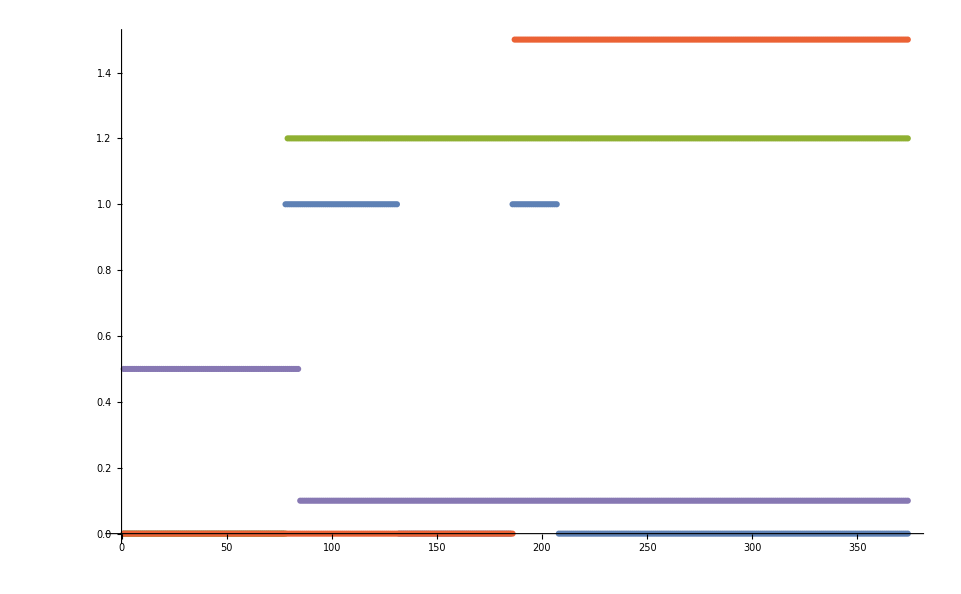

```mathematica
ListPlot[{
#["jump"]& /@ botinput,
#["jump"]& /@ inputs,
(#["jumped"]& /@ car) /. {True->1.2, False->0},
(#["double_jumped"]& /@ car)/. {True->1.5, False->0},
(#["has_wheel_contact"]& /@ car)/. {True->0.5, False->0.1}
}, PlotRange->All]
```